## Introduction

### Tag Systems and Their Motivation

### Multi-Way Tag Systems

### Wolfram Language Implementation

I’ll write system specifications in the following form:

```mathematica
postSystem = {v -> 3, 0 -> {0, 0}, 1 -> {1, 1, 0, 1}};
multiPostSystem = postSystem ~Join~ {1 -> {1, 1, 1, 0}, 1 -> {0, 1, 1, 1}, 1 -> {1, 0, 1, 1}};
rabbitSystem = {v -> 1, 0 -> {0}, 0 -> {1, 0}, 1 -> {}};
```

First, I’ll implement evolution of MWTSes by transforming system specifications to replacement rules.

```mathematica
systemToReplacementRules[system:{v -> v_Integer, productionSpec___}] :=
	{productionSpec} /. (HoldPattern[head_ -> tail_List] :> 
		Flatten[{head, ConstantArray[_, v - 1], w___}] :> Join[{w}, tail])

evolveSystem[system_List] := evolveSystem[system, #]&
evolveSystem[system_List,state_List] := Flatten[ReplaceList[systemToReplacementRules[system]] /@ state, 1]
```

Then I can plot a graph of how these systems evolve:

```mathematica
stateGraph[system_List, init_List, maxIters_:Infinity] := ResourceFunction["FixedPointGraph"][ReplaceList[systemToReplacementRules[system]], init, maxIters]
stateGraphPlot[system_List, init_List, maxIters_:Infinity, opts:OptionsPattern[]] := GraphPlot[
	stateGraph[system, init, maxIters],
	VertexLabels -> v_ :> Placed[StringJoin @@ ToString /@ v, Tooltip],
	opts
]
```

For example, here’s a graph of the “rabbit system,” which I’ll talk more about later, starting with all strings at most ten characters long and containing exactly one zero.

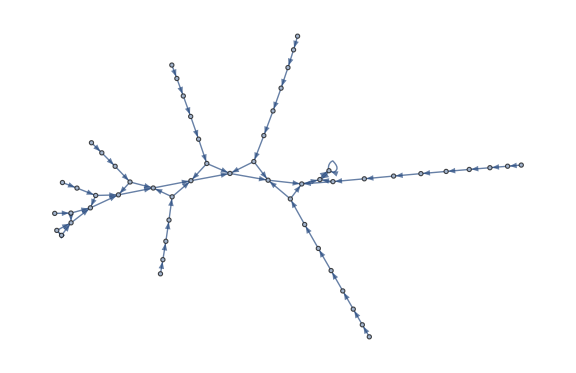
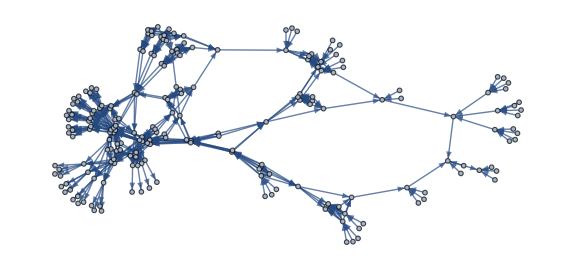

```mathematica
Row[{
stateGraphPlot[rabbitSystem, Flatten[Permutations[Prepend[ConstantArray[1, #], 0]]& /@ Range[9], 1], 3, ImageSize -> Large],
stateGraphPlot[multiPostSystem, Flatten[Tuples[{0, 1}, #]& /@ Range[3, 6], 1], 3, ImageSize -> Large]
}]
```

## Properties of Deterministic 1-Tag Systems

### 1-Tag Systems are Not Context-Free

It’s well known that, unlike other tag systems, 1-tag systems are not Turing-complete, but do they produce regular languages?

Let’s look at the 1-tag system defined by the following rules:

```mathematica
exponentialRules = {v -> 1, a -> {a, a}, b -> {b}};
```

That is, the first symbol of the string is doubled and moved to the end of the string.
Starting with the string “ab”, let’s look at how the system evolves:

```mathematica
NestList[Replace[systemToReplacementRules[exponentialRules]],{a, b},10]/. (w:{a.., b} :> Style[w, RGBColor[0.1, 0.4, 0.8]]) // Column
```

{a,b}
{b,a,a}
{a,a,b}
{a,b,a,a}
{b,a,a,a,a}
{a,a,a,a,b}
{a,a,a,b,a,a}
{a,a,b,a,a,a,a}
{a,b,a,a,a,a,a,a}
{b,a,a,a,a,a,a,a,a}
{a,a,a,a,a,a,a,a,b}

I’ve colored in blue the words which take the form , which are also the “generations” of the system.

Now let’s assume for the sake of contradiction that the set of words produced by this automaton is a context-free grammar. Then its intersection with the regular grammar  is also context-free. But we can clearly see that this intersection is the grammar , which is context-sensitive.

### FSM Generation of Strings by Binarized Digit Index

## Multi-Way Tag Systems

### Enumeration of Tag Systems

To get an idea of how these systems behave, I’ve implemented a function that can simply list out every possible tag system with a certain deletion number, alphabet, rule count, and maximum append length.

```mathematica
enumerateSystems[del_Integer, abc_List, rules_Integer, suf_Integer] := Module[{ruleLhsLists, ruleRhsLists, productionSpecs},
ruleLhsLists = Flatten @* MapIndexed[ConstantArray[abc[[#2]], #1]&] /@ IntegerPartitions[rules, {Length[abc]}];
ruleRhsLists = Tuples[Flatten[Tuples[abc, #]& /@ Range[0, suf], 1], rules];
productionSpecs = Flatten[Table[Thread[lhsList -> rhsList], {lhsList, ruleLhsLists}, {rhsList, ruleRhsLists}], 1];
DeleteDuplicates[Prepend[v -> del] @* Sort /@ productionSpecs]
]
```

For example, we can count the number of binary tag systems “at most as simple” as Post’s original tag system by looking at all the binary tag systems with only two rules and adding at most four symbols to the end in each rule.

```mathematica
enumerateSystems[3, Range[2], 2, 4] // Length
```

961

Let’s take a look at some of the simplest tag systems, with only one symbol.

### Singleton Alphabets and Linear Diophantine Equations

If there’s only a single symbol in the alphabet, then words are completely determined by their length. In this case, tag operations simply change the length of the word by adding an integer value. For example, the tag system defined by  can either subtract one or add two at each iteration. This gives us that the language of strings generated by the system from the initial string  is , where  satisfies the Diophantine equation  with . In general, any tag system with only one symbol in its alphabet can be rewritten as a linear Diophantine equation (in one variable, for deterministic tag systems).

Here are state graphs for ten of the simplest tag systems over the alphabet .

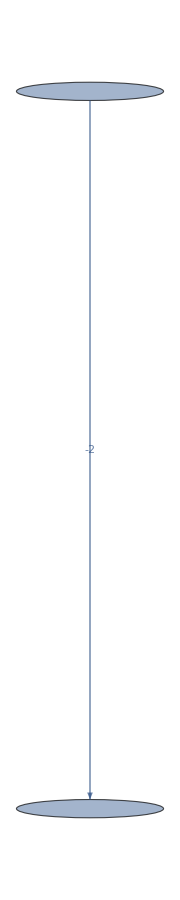
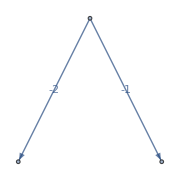
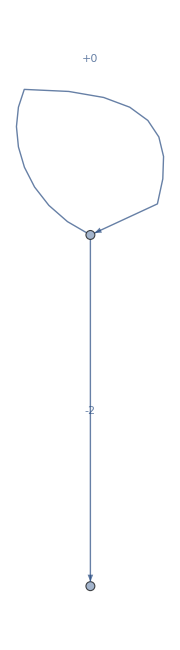
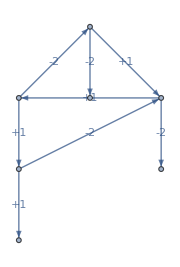
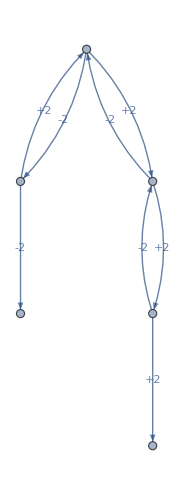
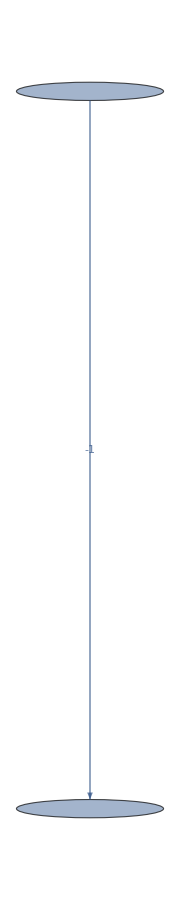
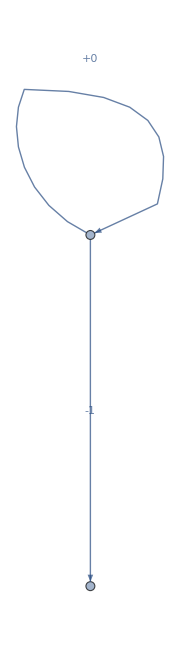
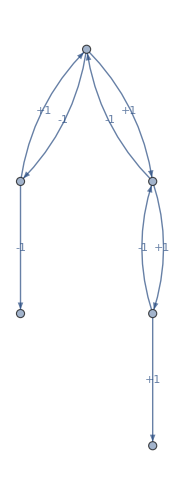

```mathematica
Row[stateGraphPlot[#, {{0, 0}}, 4,
GraphLayout->"LayeredEmbedding",
EdgeLabels->{x_ ->y_ :> NumberForm[Length[y] - Length[x], NumberSigns->{"-", "+"}]},
EdgeStyle->{x_->y_ :> Hue[0.3 * (Length[x] - Length[y])]},
ImageSize->Small
]& /@ enumerateSystems[2, {0}, 2, 4], Spacer[30]]
```

### Larger Alphabets

Systems over larger alphabets exhibit much more complex behavior. I’ll start by enumerating the smallest class of systems with a binary alphabet and one non-deterministic rule.

```mathematica
simpleSystems = enumerateSystems[2, {0, 1}, 3, 3];
Length[simpleSystems]
```

1800

A lot of these tag systems are uninteresting in the sense that their words either always grow or always shrink. I’ll start by looking at systems with some rules that shrink the string and some that grow it. This greatly reduces the number of systems.

```mathematica
simpleDynamicSystems = Select[
simpleSystems,
With[{rhsLens =Length /@ Values[Rest[#]]},Min[rhsLens] < 2 && Max[rhsLens] > 2
]&
];
Length[simpleDynamicSystems]
```

708

```mathematica
Manipulate[Column[{
simpleSystems[[i]],
Spacer[10],
stateGraphPlot[simpleDynamicSystems[[i]], {{0, 0}, {1, 0}}, s, ImageSize->Medium]
}], {i, 1, Length[simpleDynamicSystems], 1}, {{s, 4}, 1, 20, 1}]
```

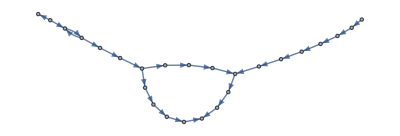

```mathematica
stateGraphPlot[simpleSystems[[420]], {{0, 0}, {1, 0}}, 10]
```

### Examining Growth

Now, within this big space of 1800 tag systems, we want to find systems with interesting behavior. One thing that might be interesting is to measure how fast the number of strings grows.

```mathematica
mwtsGrowth[system_List, init_List, iters_Integer] := Length /@ NestList[DeleteDuplicates @* evolveSystem[system], init, iters]
```

We can start by plotting how the number of unique strings produced by the system grows as we continue applying the production rules. It’s very common for these systems to grow exponentially, so I’ve used a logarithmic scale.

```mathematica
simpleDynamicSystemGrowth = mwtsGrowth[#, {{0, 0}, {1, 0}}, 20]& /@  simpleDynamicSystems;
```

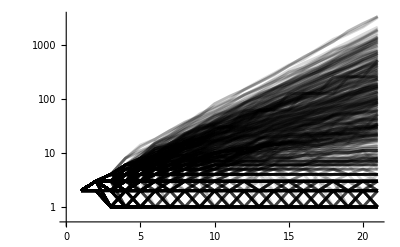

```mathematica
ListLogPlot[
Table[
Style[
Tooltip[
simpleDynamicSystemGrowth[[i]],
ToString[i]
],
Opacity[0.15, Black]
],
{i, Length[simpleDynamicSystemGrowth]}],
Joined->True,
ImageSize->Full
]
```

As we can see, there are a lot of roughly exponential systems (linear, on the log plot) and finite systems which only every reach a finite set of strings (horizontal lines, on the plot). What’s most interesting, though, are the ones in between the two extremes.

{v→2,0→{0,1,0},0→{1,0,1},1→{}}

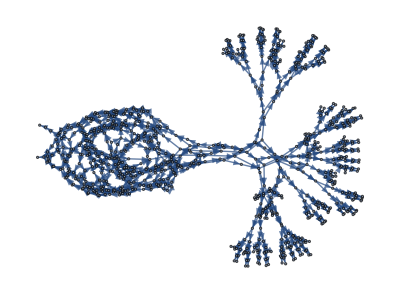

```mathematica
simpleDynamicSystems[[655]]
stateGraphPlot[simpleDynamicSystems[[655]], {{0, 0}}, 20]
```

### The Double Helical System

```mathematica
doubleHelicalSystem = simpleDynamicSystems[[199]]
GraphPlot[stateGraph[doubleHelicalSystem, {{1, 0}}, 10]]
```

{v→2,0→{0},0→{0,0},1→{1,1,0}}

-Graphics-

```mathematica
e=EdgeList[stateGraph[doubleHelicalSystem, {{1, 0}}, 10]]/.x_->y_->{x,y}
```

{{{1,0},{1,1,0}},{{1,0,0},{0,1,1,0}},{{1,1,0},{0,1,1,0}},{{0,1,1,0},{1,0,0}},{{0,1,1,0},{1,0,0,0}},{{1,0,0,0},{0,0,1,1,0}},{{1,1,0,0},{0,0,1,1,0}},{{0,0,1,1,0},{1,1,0,0}},{{0,0,1,1,0},{1,1,0,0,0}},{{0,1,1,0,0},{1,0,0,0}},{{0,1,1,0,0},{1,0,0,0,0}},{{1,0,0,0,0},{0,0,0,1,1,0}},{{1,1,0,0,0},{0,0,0,1,1,0}},{{0,0,0,1,1,0},{0,1,1,0,0}},{{0,0,0,1,1,0},{0,1,1,0,0,0}},{{0,1,1,0,0,0},{1,0,0,0,0}},{{0,1,1,0,0,0},{1,0,0,0,0,0}},{{1,0,0,0,0,0},{0,0,0,0,1,1,0}},{{0,0,0,0,1,1,0},{0,0,1,1,0,0}},{{0,0,0,0,1,1,0},{0,0,1,1,0,0,0}}}

```mathematica
tagSystemToModel[tagSystem_,updateEvents_]:=
Table[
EdgeList[stateGraph[tagSystem, {{1, 0}}, i]]/.x_->y_->{x,y}
,{i, updateEvents}]
```

```mathematica
key =DeleteDuplicates[Flatten[tagSystemToModel[doubleHelicalSystem,15],2]]
```

{{1,0},{1,1,0},{0,1,1,0},{1,0,0},{1,0,0,0},{0,0,1,1,0},{1,1,0,0},{1,1,0,0,0},{0,0,0,1,1,0},{0,1,1,0,0},{0,1,1,0,0,0},{1,0,0,0,0},{1,0,0,0,0,0},{0,0,0,0,1,1,0},{0,0,1,1,0,0},{0,0,1,1,0,0,0},{1,1,0,0,0,0},{1,1,0,0,0,0,0},{0,0,0,0,0,1,1,0},{0,0,0,1,1,0,0},{0,0,0,1,1,0,0,0},{0,1,1,0,0,0,0},{0,1,1,0,0,0,0,0},{1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0}}

```mathematica
key =Table[
key[[i]]->i
,{i, Length[key]}]
```

{{1,0}→1,{1,1,0}→2,{0,1,1,0}→3,{1,0,0}→4,{1,0,0,0}→5,{0,0,1,1,0}→6,{1,1,0,0}→7,{1,1,0,0,0}→8,{0,0,0,1,1,0}→9,{0,1,1,0,0}→10,{0,1,1,0,0,0}→11,{1,0,0,0,0}→12,{1,0,0,0,0,0}→13,{0,0,0,0,1,1,0}→14,{0,0,1,1,0,0}→15,{0,0,1,1,0,0,0}→16,{1,1,0,0,0,0}→17,{1,1,0,0,0,0,0}→18,{0,0,0,0,0,1,1,0}→19,{0,0,0,1,1,0,0}→20,{0,0,0,1,1,0,0,0}→21,{0,1,1,0,0,0,0}→22,{0,1,1,0,0,0,0,0}→23,{1,0,0,0,0,0,0}→24,{1,0,0,0,0,0,0,0}→25}

```mathematica
thing = tagSystemToModel[doubleHelicalSystem,15]/.key
```

{{{1,2}},{{1,2},{2,3}},{{1,2},{2,3},{3,4},{3,5}},{{1,2},{4,3},{2,3},{3,4},{3,5},{5,6}},{{1,2},{4,3},{2,3},{3,4},{3,5},{5,6},{6,7},{6,8}},{{1,2},{4,3},{2,3},{3,4},{3,5},{5,6},{7,6},{6,7},{6,8},{8,9}},{{1,2},{4,3},{2,3},{3,4},{3,5},{5,6},{7,6},{6,7},{6,8},{8,9},{9,10},{9,11}},{{1,2},{4,3},{2,3},{3,4},{3,5},{5,6},{7,6},{6,7},{6,8},{10,5},{10,12},{8,9},{9,10},{9,11},{11,12},{11,13}},{{1,2},{4,3},{2,3},{3,4},{3,5},{5,6},{7,6},{6,7},{6,8},{10,5},{10,12},{12,9},{8,9},{9,10},{9,11},{11,12},{11,13},{13,14}},{{1,2},{4,3},{2,3},{3,4},{3,5},{5,6},{7,6},{6,7},{6,8},{10,5},{10,12},{12,9},{8,9},{9,10},{9,11},{11,12},{11,13},{13,14},{14,15},{14,16}},{{1,2},{4,3},{2,3},{3,4},{3,5},{5,6},{7,6},{6,7},{6,8},{10,5},{10,12},{12,9},{8,9},{9,10},{9,11},{15,8},{15,17},{11,12},{11,13},{13,14},{14,15},{14,16},{16,17},{16,18}},{{1,2},{4,3},{2,3},{3,4},{3,5},{5,6},{7,6},{6,7},{6,8},{10,5},{10,12},{12,9},{8,9},{9,10},{9,11},{15,8},{15,17},{11,12},{11,13},{13,14},{17,14},{14,15},{14,16},{16,17},{16,18},{18,19}},{{1,2},{4,3},{2,3},{3,4},{3,5},{5,6},{7,6},{6,7},{6,8},{10,5},{10,12},{12,9},{8,9},{9,10},{9,11},{15,8},{15,17},{11,12},{11,13},{13,14},{17,14},{14,15},{14,16},{16,17},{16,18},{18,19},{19,20},{19,21}},{{1,2},{4,3},{2,3},{3,4},{3,5},{5,6},{7,6},{6,7},{6,8},{10,5},{10,12},{12,9},{8,9},{9,10},{9,11},{15,8},{15,17},{11,12},{11,13},{13,14},{17,14},{14,15},{14,16},{20,11},{20,22},{16,17},{16,18},{18,19},{19,20},{19,21},{21,22},{21,23}},{{1,2},{4,3},{2,3},{3,4},{3,5},{5,6},{7,6},{6,7},{6,8},{10,5},{10,12},{12,9},{8,9},{9,10},{9,11},{15,8},{15,17},{11,12},{11,13},{13,14},{17,14},{14,15},{14,16},{20,11},{20,22},{16,17},{16,18},{22,13},{22,24},{18,19},{19,20},{19,21},{21,22},{21,23},{23,24},{23,25}}}